## Teorema de continuidad de Lévy (Teorema central del límite de De Moivre)

#### Ejemplo: Binomial estandarizadas a Normal (0,1); (X_n-n p)/(√(n p q))→^d 𝒩(0,1), donde X_n\[Distributed]ℬ(n,p)

Mediante propiedades de la función característica

Comando: CharacteristicFunction

```mathematica
ⅇ^((-n p ⅈ)/(√(n p(1-p))))CharacteristicFunction[BinomialDistribution[n,p],t/(√(n p(1-p)))]
```

ⅇ^(-(ⅈ n p)/(√(n (1-p) p))) (1-p+ⅇ^((ⅈ t)/(√(n (1-p) p))) p)^n

Construyendo el modelo   (X_n-n p)/(√(n p(1-p))), donde X_n\[Distributed]ℬ(n,p)

Comando: TransformedDistribution

```mathematica
Binomialestandar[n_,p_]:=TransformedDistribution[(Xn-n p)/(√(n p(1-p))),Xn\[Distributed]BinomialDistribution[n,p]]
```

Función característica del modelo

```mathematica
CharacteristicFunction[Binomialestandar[n,p],t]
```

ⅇ^(-(ⅈ n p t)/(√(n (1-p) p))) (1-p+ⅇ^((ⅈ t)/(√(n (1-p) p))) p)^n

Función característica para  p=1/2

```mathematica
CharacteristicFunction[Binomialestandar[n,1/2],t]
```

ⅇ^(-ⅈ √n t) (1/2+1/2 ⅇ^((2 ⅈ t)/(√n)))^n

Gráfica de la función característica para  p=1/2, al ser simétrica la función de probabilidad, debe ser real

Para p=1/2, el soporte de la distribución es  -√n≤ x≤ √n, con diferencia de 2/(√n)

```mathematica
pdfBinomialestandar[n_,p_,x_]:=PDF[BinomialDistribution[n,p],Chop[x √(n p (1-p))+n p,0.1]]
```

```mathematica
pdfBinomialestandar[20,1/3,17/√20]
```

0

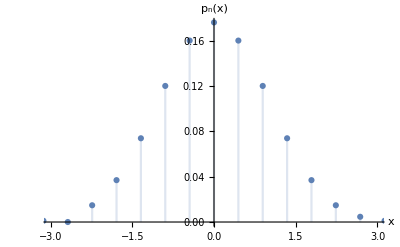

```mathematica
DiscretePlot[pdfBinomialestandar[20,1./2,x],{x,-√20.,√20.,2/√20.},
PlotRange->{{-3,3},All},AxesOrigin->{0,0},AxesLabel->{x,Subscript[p, n][x]}]
```

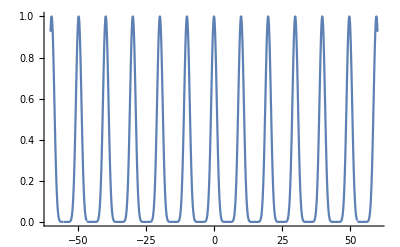

```mathematica
Plot[CharacteristicFunction[Binomialestandar[10,1/2],t],{t,-60,60},PlotRange->All]
```

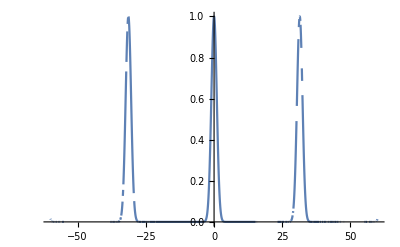

```mathematica
Plot[CharacteristicFunction[Binomialestandar[100,1/2],t],{t,-60,60},PlotRange->All]
```

General::munfl: (0.102863+0.30378 ⅈ)^1000 is too small to represent as a normalized machine number; precision may be lost.

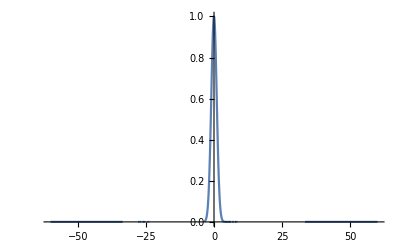

```mathematica
Plot[CharacteristicFunction[Binomialestandar[1000,1/2],t],{t,-60,60},PlotRange->All]
```

Límite de φ_n

Comando: DiscreteLimit

```mathematica
DiscreteLimit[CharacteristicFunction[Binomialestandar[n,1/2],t],n->∞]
```

ⅇ^(-t^2/2)

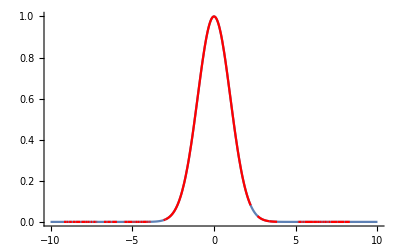

```mathematica
Show[Plot[CharacteristicFunction[NormalDistribution[],t],{t,-10,10},PlotRange->All],Plot[CharacteristicFunction[Binomialestandar[1000,1/2],t],{t,-10,10},PlotStyle->Red,PlotRange->All]]
```

Gráfica de la función característica para  p=1/3

Para p=1/3, el soporte es  -√(n/2)≤ x≤ √(2n), con diferencia de 3/(√(2n))

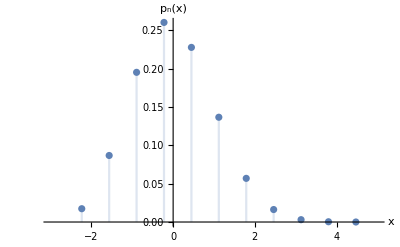

```mathematica
DiscretePlot[pdfBinomialestandar[10,1/3,x],{x,-√5,√20,3/√20},
PlotRange->{{-3,5},All},AxesOrigin->{0,0},AxesLabel->{x,Subscript[p, n][x]}]
```

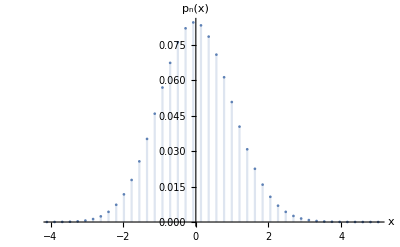

```mathematica
DiscretePlot[pdfBinomialestandar[100,1/3,x],{x,-√50,√200,3/√200},
PlotRange->{{-4,5},All},AxesOrigin->{0,0},AxesLabel->{x,Subscript[p, n][x]}]
```

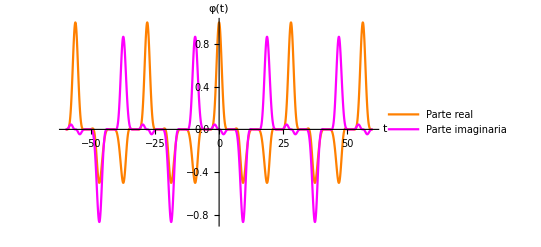

```mathematica
Plot[{Re[CharacteristicFunction[Binomialestandar[10,1/3],t]],Im[CharacteristicFunction[Binomialestandar[10,1/3],t]]},{t,-60,60},PlotStyle->{Orange,Magenta},AxesLabel->{t,φ[t]},PlotRange->Full,PlotLegends->{"Parte real","Parte imaginaria"}]
```

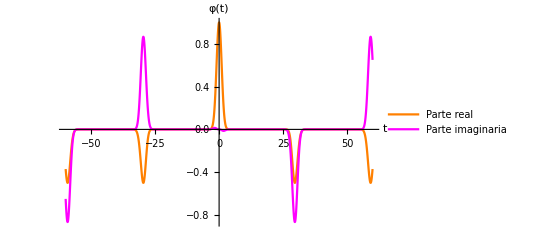

```mathematica
Plot[{Re[CharacteristicFunction[Binomialestandar[100,1/3],t]],Im[CharacteristicFunction[Binomialestandar[100,1/3],t]]},{t,-60,60},PlotStyle->{Orange,Magenta},AxesLabel->{t,φ[t]},PlotRange->Full,PlotLegends->{"Parte real","Parte imaginaria"}]
```

```mathematica
Plot[{Re[CharacteristicFunction[Binomialestandar[1000,1/3],t]],Im[CharacteristicFunction[Binomialestandar[1000,1/3],t]]},{t,-60,60},PlotStyle->{Orange,Magenta},AxesLabel->{t,φ[t]},PlotRange->Full,PlotLegends->{"Parte real","Parte imaginaria"}]
```

```mathematica
DiscreteLimit[CharacteristicFunction[Binomialestandar[n,1/3],t],n->∞]
```

ⅇ^(-t^2/2)

```mathematica
DiscreteLimit[CharacteristicFunction[Binomialestandar[n,p],t],n->∞]
```

ⅇ^(-t^2/2)